```mathematica
ClearAll["Global`*"]
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhotonEP[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonEPAnal[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/2 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(2 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]

MapThread[Themes`AddThemeRules["LogGrid",#,GridLines->#2,Frame->True]&,{{LogPlot|ListLogPlot,LogLinearPlot|ListLogLinearPlot,LogLogPlot|ListLogLogPlot},{{Automatic,logticks},{logticks,Automatic},logticks}}];
```

```mathematica
Clear[g,χ]
FEP2=QFInoDisp[2,χ,χ]
LeadingOrderCheck[Fcov2,Fdisp2,n2,2]
```

4+4 t^2 χ^2

leading order covariant 16 χ^4

True

leading order displacement 32 (p1^2+x2^2) χ^4

True

leading order mean photon number  2 (2+p1^2+x2^2) χ^2

True

```mathematica
QFI2pp=(Fcov2+Fdisp2)/n2/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify;
Q2=QFI2pp/.{t^2 χ^2->χeff^2}
Fcov2+Fdisp2/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
```

4+4 χeff^2

16 (t^2 χ^2+t^4 χ^4)

```mathematica
Clear[g,χ]
{Fcov3,Fdisp3,n3}=QFIperPhotonEP[3]
QFIperPhotonEPAnal[3]
LeadingOrderCheck[Fcov3,Fdisp3,n3,3]
```

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (4+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (2+p1^2+x3^2) χ^4)}

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (4+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (2+p1^2+x3^2) χ^4)}

leading order covariant 16 χ^8

True

leading order displacement 32 (p1^2+x3^2) χ^8

True

leading order mean photon number  2 (2+p1^2+x3^2) χ^4

True

```mathematica
QFI3pp=(Fcov3+Fdisp3)/n3/.{x1->0,x2->0,x3->0,p1->0,p2->0,p3->0}//FullSimplify
Q3=QFI3pp/.{t^2 χ^2->χeff^2}
Fcov3+Fdisp3/.{x1->0,x2->0,x3->0,p1->0,p2->0,p3->0}//FullSimplify
```

4 (1+t^2 χ^2)^2

4 (1+χeff^2)^2

16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2

```mathematica
Clear[g,χ]
{Fcov4,Fdisp4,n4}=QFIperPhotonEPAnal[4]
LeadingOrderCheck[Fcov4,Fdisp4,n4,4]
```

{48 t^2 χ^2+16/81 t^4 χ^4 (729+900 t^2 χ^2+522 t^4 χ^4+144 t^6 χ^6+16 t^8 χ^8),2/81 (81 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-648 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+324 t^2 (3 p1^2+4 p1 p3+4 p3^2+(2 p2+p4)^2+4 x2^2+(x1+2 x3)^2+4 x2 x4+3 x4^2) χ^2-216 t^3 (21 p1 p2+24 p2 p3+8 p1 p4+9 p3 p4-9 x1 x2-24 x2 x3-8 x1 x4-21 x3 x4) χ^3+108 t^4 (45 p2^2+3 (p1+p3) (11 p1+9 p3)+28 p2 p4+3 p4^2+3 x1^2+28 x1 x3+45 x3^2+3 (x2+x4) (9 x2+11 x4)) χ^4-432 t^5 (4 p3 (5 p2+p4)+p1 (26 p2+7 p4)-4 x2 (x1+5 x3)-(7 x1+26 x3) x4) χ^5+144 t^6 (42 p2^2+3 (p1+p3) (14 p1+5 p3)+15 p2 p4+p4^2+x1^2+15 x1 x3+42 x3^2+3 (x2+x4) (5 x2+14 x4)) χ^6-576 t^7 (19 p1 p2+9 p2 p3+3 p1 p4+p3 p4-x1 x2-9 x2 x3-3 x1 x4-19 x3 x4) χ^7+144 t^8 (33 p1^2+21 p2^2+28 p1 p3+4 p3^2+4 p2 p4+4 x2^2+4 x1 x3+21 x3^2+28 x2 x4+33 x4^2) χ^8-384 t^9 (3 p2 (4 p1+p3)+p1 p4-x1 x4-3 x3 (x2+4 x4)) χ^9+192 t^10 (9 p1^2+4 p1 p3+3 (p2^2+x3^2)+4 x2 x4+9 x4^2) χ^10+768 t^11 (-p1 p2+x3 x4) χ^11+256 t^12 (p1^2+x4^2) χ^12),1/2 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-2 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+2 t^2 (6+p1^2+p1 p3+p3^2+p2 (p2+p4)+x2^2+x3 (x1+x3)+x2 x4+x4^2) χ^2-4/3 t^3 (3 p2 (p1+p3)+p1 p4-x1 x4-3 x3 (x2+x4)) χ^3+2/3 t^4 (3 p1^2+4 p1 p3+3 (4+p2^2+x3^2)+4 x2 x4+3 x4^2) χ^4+8/3 t^5 (-p1 p2+x3 x4) χ^5+8/9 t^6 (2+p1^2+x4^2) χ^6}

leading order covariant (256 χ^12)/81

True

leading order displacement 512/81 (p1^2+x4^2) χ^12

True

leading order mean photon number  8/9 (2+p1^2+x4^2) χ^6

True

```mathematica
QFI4pp=(Fcov4+Fdisp4)/n4/.{x1->0,x2->0,x3->0,x4->0,p1->0,p2->0,p3->0,p4->0}//FullSimplify
Q4=QFI4pp/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6}
Fcov4+Fdisp4/.{x1->0,x2->0,x3->0,x4->0,p1->0,p2->0,p3->0,p4->0}//FullSimplify
```

1+10 t^2 χ^2+8 t^4 χ^4+(16 t^6 χ^6)/9+(9 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

1+10 χeff^2+8 χeff^4+(16 χeff^6)/9+(9 (9+4 χeff^2))/(27+18 χeff^2+4 χeff^4)

48 t^2 χ^2+16/81 t^4 χ^4 (729+900 t^2 χ^2+522 t^4 χ^4+144 t^6 χ^6+16 t^8 χ^8)

```mathematica
{Fcov5,Fdisp5,n5}=QFIperPhotonEPAnal[5]
LeadingOrderCheck[Fcov5,Fdisp5,n5,5]
```

{16/81 t^2 χ^2 (3+t^2 χ^2) (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8)),2/81 (81 (p1^2+p2^2+p3^2+p4^2+p5^2+x1^2+x2^2+x3^2+x4^2+x5^2)-648 t (p1 p2+p2 p3+p4 (p3+p5)-x1 x2-x3 (x2+x4)-x4 x5) χ+324 t^2 (3 p1^2+4 p1 p3+4 (p2^2+p2 p4+p4^2)+(2 p3+p5)^2+(x1+2 x3)^2+4 (x2^2+x2 x4+x4^2)+4 x3 x5+3 x5^2) χ^2-216 t^3 (24 p3 (p2+p4)+p1 (21 p2+8 p4)+(8 p2+9 p4) p5-24 x3 (x2+x4)-x1 (9 x2+8 x4)-(8 x2+21 x4) x5) χ^3+108 t^4 (33 p1^2+45 p2^2+60 p1 p3+48 p3^2+64 p2 p4+27 p4^2+16 p1 p5+28 p3 p5+3 p5^2+3 x1^2+27 x2^2+28 x1 x3+48 x3^2+64 x2 x4+45 x4^2+16 x1 x5+60 x3 x5+33 x5^2) χ^4-216 t^5 (52 p1 p2+62 p2 p3+31 p1 p4+42 p3 p4+15 p2 p5+8 p4 p5-8 x1 x2-42 x2 x3-15 x1 x4-62 x3 x4-31 x2 x5-52 x4 x5) χ^5+72 t^6 (84 p1^2+114 p2^2+96 p3^2+132 p2 p4+32 p4^2+33 p3 p5+2 p5^2+9 p1 (19 p3+4 p5)+2 x1^2+32 x2^2+33 x1 x3+96 x3^2+132 x2 x4+114 x4^2+36 x1 x5+171 x3 x5+84 x5^2) χ^6-144 t^7 (99 p1 p2+97 p2 p3+51 p1 p4+43 p3 p4+5 (3 p2+p4) p5-43 x2 x3-97 x3 x4-5 x1 (x2+3 x4)-51 x2 x5-99 x4 x5) χ^7+36 t^8 (163 p1^2+112 p3^2+4 (47 p2^2+38 p2 p4+6 p4^2)+24 p3 p5+p5^2+8 p1 (36 p3+5 p5)+x1^2+4 (6 x2^2+28 x3^2+38 x2 x4+47 x4^2)+288 x3 x5+163 x5^2+8 x1 (3 x3+5 x5)) χ^8-48 t^9 (201 p1 p2+144 p2 p3+74 p1 p4+42 p3 p4+14 p2 p5+3 p4 p5-3 x1 x2-42 x2 x3-14 x1 x4-144 x3 x4-74 x2 x5-201 x4 x5) χ^9+48 t^10 (69 p1^2+60 p2^2+32 p2 p4+3 p4^2+3 p3 (8 p3+p5)+p1 (91 p3+8 p5)+3 x2^2+3 x3 (x1+8 x3)+32 x2 x4+60 x4^2+(8 x1+91 x3) x5+69 x5^2) χ^10-96 t^11 (3 p3 (6 p2+p4)+p1 (37 p2+9 p4)+p2 p5-3 x2 (x3+3 x5)-x4 (x1+18 x3+37 x5)) χ^11+16 t^12 (67 p1^2+40 p2^2+9 p3^2+12 p2 p4+3 p1 (20 p3+p5)+9 x3^2+12 x2 x4+40 x4^2+3 x1 x5+60 x3 x5+67 x5^2) χ^12-32 t^13 (22 p1 p2+6 p2 p3+3 p1 p4-6 x3 x4-3 x2 x5-22 x4 x5) χ^13+32 t^14 (2 p2^2+3 p1 (2 p1+p3)+2 x4^2+3 x5 (x3+2 x5)) χ^14+64 t^15 (-p1 p2+x4 x5) χ^15+16 t^16 (p1^2+x5^2) χ^16),1/18 (9 (p1^2+p2^2+p3^2+p4^2+p5^2+x1^2+x2^2+x3^2+x4^2+x5^2)-36 t (p1 p2+p2 p3+p4 (p3+p5)-x1 x2-x3 (x2+x4)-x4 x5) χ+36 t^2 (8+p1^2+p2^2+p1 p3+p2 p4+p4^2+p3 (p3+p5)+x2^2+x3 (x1+x3)+x2 x4+x4^2+x3 x5+x5^2) χ^2-24 t^3 (3 p3 (p2+p4)+p1 (3 p2+p4)+p2 p5-x2 (3 x3+x5)-x4 (x1+3 (x3+x5))) χ^3+12 t^4 (18+3 p1^2+3 p3^2+p2 (3 p2+4 p4)+p1 (4 p3+p5)+3 x3^2+x4 (4 x2+3 x4)+4 x3 x5+x5 (x1+3 x5)) χ^4-24 t^5 (2 p2 (p1+p3)+p1 p4-x2 x5-2 x4 (x3+x5)) χ^5+8 t^6 (2 p1^2+3 p1 p3+2 (4+p2^2+x4^2)+3 x3 x5+2 x5^2) χ^6+16 t^7 (-p1 p2+x4 x5) χ^7+4 t^8 (2+p1^2+x5^2) χ^8)}

leading order covariant (16 χ^16)/81

True

leading order displacement 32/81 (p1^2+x5^2) χ^16

True

leading order mean photon number  2/9 (2+p1^2+x5^2) χ^8

True

```mathematica
QFI5pp=(Fcov5+Fdisp5)/n5/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}//Simplify
Q5=QFI5pp/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6,t^8 χ^8->χeff^8,t^10 χ^10->χeff^10,t^12 χ^12->χeff^12}
Fcov5+Fdisp5/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}//FullSimplify
```

(4 (108+315 t^2 χ^2+387 t^4 χ^4+237 t^6 χ^6+77 t^8 χ^8+13 t^10 χ^10+t^12 χ^12))/(9 (12+5 t^2 χ^2+t^4 χ^4))

(4 (108+315 χeff^2+387 χeff^4+237 χeff^6+77 χeff^8+13 χeff^10+χeff^12))/(9 (12+5 χeff^2+χeff^4))

16/81 t^2 χ^2 (3+t^2 χ^2) (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8))

```mathematica
n2eff=n2/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6,t^8 χ^8->χeff^8}
n3eff=n3/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6,t^8 χ^8->χeff^8}
n4eff=n4/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6,t^8 χ^8->χeff^8}
n5eff=n5/.{x1->0,x2->0,x3->0,x4->0,x5->0,p1->0,p2->0,p3->0,p4->0,p5->0}/.{t^2 χ^2->χeff^2,t^4 χ^4->χeff^4,t^6 χ^6->χeff^6,t^8 χ^8->χeff^8}
```

4 χeff^2

1/2 (16 χeff^2+8 χeff^4)

12 χeff^2+8 χeff^4+(16 χeff^6)/9

1/18 (288 χeff^2+216 χeff^4+64 χeff^6+8 χeff^8)

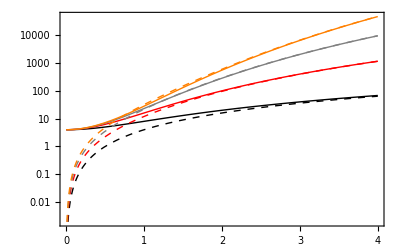

```mathematica
p=LogPlot[{Q2,Q3,Q4,Q5, n2eff, n3eff, n4eff, n5eff},{χeff,0,4},PlotStyle->{Black,Red,Gray,Orange,{Black,Dashed},{Red,Dashed},{Gray,Dashed},{Orange,Dashed}},GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full]
```

```mathematica
(*TRY TO UNDERSTAND HOW QFI SCALES WITH N FOR A BKC NOT AT AN EP*)
```

```mathematica
(* analytical calculations NOT at an EP*)
Clear[g,χ]
(*Nmodes=4;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
eigs=Eigensystem[DM]
S=Transpose[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
TrS=Inverse[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
InS=Transpose[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
InTrS=Inverse[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
Σin=CovarBasis[Nmodes].S.TrS.Transpose[CovarBasis[Nmodes]];
Σin//FullSimplify//TraditionalForm
InΣin=CovarBasis[Nmodes].InTrS.InS.Transpose[CovarBasis[Nmodes]];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Fcov=-1/2 Tr[InΣin.G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify*)

(* At EP*)
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
Fcov=-1/2 Tr[Inverse[Σin].G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify

Nmodes=5;
M=Nmodes;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
"Dynamical Matrix"
DM//MatrixForm
MatrixPower[DM,Nmodes-1]//MatrixForm
MatrixPower[DM,Nmodes-1]==SparseArray[{{1,Nmodes}->2^(Nmodes-1) χ^(Nmodes-1),{2 Nmodes,Nmodes+1}->(-1)^(Nmodes-1) 2^(Nmodes-1) χ^(Nmodes-1)},{2 Nmodes,2 Nmodes}]

DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify

Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];
Gt//TraditionalForm
MatrixPower[DM,Nmodes-1].Gt.MatrixPower[DM,Nmodes-1]//MatrixForm
MatrixPower[Transpose[DM],Nmodes-1].Gt.MatrixPower[Transpose[DM],Nmodes-1]//MatrixForm
MatrixPower[DM,M-1].Gt.MatrixPower[DM,M-1].MatrixPower[Transpose[DM],M-1].Gt.MatrixPower[Transpose[DM],M-1]//MatrixForm

"Actual leading term"
-Tr[1/2 1/((M-1)!)^4 MatrixPower[DM,M-1].Gt.MatrixPower[DM,M-1].MatrixPower[Transpose[DM],M-1].Gt.MatrixPower[Transpose[DM],M-1]]//FullSimplify

"Calculated"
 1/((M-1)!)^4 (2^(M-1))^4 (χ^(M-1))^4

"photon number analytical formula"
nForm=1/(4 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]])//FullSimplify
nForm==1/(4 ((M-1)!)^2)(Tr[MatrixPower[DM,M-1].MatrixPower[Transpose[DM],M-1]])
MatrixPower[DM,Nmodes-1].MatrixPower[Transpose[DM],Nmodes-1]//MatrixForm
1/2 (2^(M-1))^2 ((χ^(M-1))^2)/((M-1)!)^2
 (2^(2M-3)) ((χ^(M-1))^2)/((M-1)!)^2
```

(4/9 t^2 χ^2 (t^6 χ^6+4 t^4 χ^4+9 t^2 χ^2+9)+1 | 0 | (8 t^7 χ^7)/9+(8 t^5 χ^5)/3+4 t^3 χ^3+2 t χ | 0 | 2/3 t^2 χ^2 (2 t^4 χ^4+4 t^2 χ^2+3) | 0 | 4/3 (t^5 χ^5+t^3 χ^3) | 0 | (2 t^4 χ^4)/3 | 0
0 | 1 | 0 | -2 t χ | 0 | 2 t^2 χ^2 | 0 | -4/3 t^3 χ^3 | 0 | (2 t^4 χ^4)/3
(8 t^7 χ^7)/9+(8 t^5 χ^5)/3+4 t^3 χ^3+2 t χ | 0 | (16 t^6 χ^6)/9+4 t^4 χ^4+4 t^2 χ^2+1 | 0 | (8 t^5 χ^5)/3+4 t^3 χ^3+2 t χ | 0 | (8 t^4 χ^4)/3+2 t^2 χ^2 | 0 | (4 t^3 χ^3)/3 | 0
0 | -2 t χ | 0 | 4 t^2 χ^2+1 | 0 | -2 t χ (2 t^2 χ^2+1) | 0 | (8 t^4 χ^4)/3+2 t^2 χ^2 | 0 | -4/3 (t^5 χ^5+t^3 χ^3)
2/3 t^2 χ^2 (2 t^4 χ^4+4 t^2 χ^2+3) | 0 | (8 t^5 χ^5)/3+4 t^3 χ^3+2 t χ | 0 | (2 t^2 χ^2+1)^2 | 0 | 4 t^3 χ^3+2 t χ | 0 | 2 t^2 χ^2 | 0
0 | 2 t^2 χ^2 | 0 | -2 t χ (2 t^2 χ^2+1) | 0 | (2 t^2 χ^2+1)^2 | 0 | -2/3 t χ (4 t^4 χ^4+6 t^2 χ^2+3) | 0 | 2/3 t^2 χ^2 (2 t^4 χ^4+4 t^2 χ^2+3)
4/3 (t^5 χ^5+t^3 χ^3) | 0 | (8 t^4 χ^4)/3+2 t^2 χ^2 | 0 | 4 t^3 χ^3+2 t χ | 0 | 4 t^2 χ^2+1 | 0 | 2 t χ | 0
0 | -4/3 t^3 χ^3 | 0 | (8 t^4 χ^4)/3+2 t^2 χ^2 | 0 | -2/3 t χ (4 t^4 χ^4+6 t^2 χ^2+3) | 0 | (16 t^6 χ^6)/9+4 t^4 χ^4+4 t^2 χ^2+1 | 0 | -2/9 t χ (4 t^6 χ^6+12 t^4 χ^4+18 t^2 χ^2+9)
(2 t^4 χ^4)/3 | 0 | (4 t^3 χ^3)/3 | 0 | 2 t^2 χ^2 | 0 | 2 t χ | 0 | 1 | 0
0 | (2 t^4 χ^4)/3 | 0 | -4/3 (t^5 χ^5+t^3 χ^3) | 0 | 2/3 t^2 χ^2 (2 t^4 χ^4+4 t^2 χ^2+3) | 0 | -2/9 t χ (4 t^6 χ^6+12 t^4 χ^4+18 t^2 χ^2+9) | 0 | 4/9 t^2 χ^2 (t^6 χ^6+4 t^4 χ^4+9 t^2 χ^2+9)+1)

(4 (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8)))/(9 (12+5 t^2 χ^2+t^4 χ^4))

Dynamical Matrix

(0 | 2 χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 χ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 χ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 χ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 χ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 χ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 χ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 χ | 0)

(0 | 0 | 0 | 0 | 16 χ^4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16 χ^4 | 0 | 0 | 0 | 0)

True

(16 χ^16)/81

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 256 χ^8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -256 χ^8 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 256 χ^8
-256 χ^8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(-65536 χ^16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -65536 χ^16)

Actual leading term

(16 χ^16)/81

Calculated

(16 χ^16)/81

photon number analytical formula

(2 χ^8)/9

True

(256 χ^8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 256 χ^8)

(2 χ^8)/9

(2 χ^8)/9

```mathematica
64 64
```

4096

```mathematica
(*positives*)
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];

DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DM//FullSimplify//TraditionalForm

"First block"
T1=DM[[1;;Nmodes,1;;Nmodes]]//FullSimplify;
T1//Eigensystem;

T2=DM[[Nmodes+1;;2 Nmodes,Nmodes+1;;2 Nmodes]]//FullSimplify;
T2==-Transpose[T1]//FullSimplify
"Matrix exponential"
(*MatrixExp[T1].Transpose[MatrixExp[T1]]//FullSimplify//MatrixForm*)


"Say χ>g"
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}]
x=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{k,1,Nmodes},{h,1,Nmodes}];
"x matrix"
x//MatrixForm
y=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{h,1,Nmodes},{k,1,Nmodes}];
"y matrix"
y//MatrixForm
"y.y^T"
y.Transpose[y]//FullSimplify//MatrixForm
y.Transpose[y]==Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Sum[((χ+g)/(χ-g))^m Sin[(h m π)/(Nmodes+1)] Sin[(k m π)/(Nmodes+1)],{m,1,Nmodes}]//Simplify],{h,1,Nmodes},{k,1,Nmodes}]//FullSimplify
"Table of sines"
Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Sum[Sin[(h m π)/(Nmodes+1)] Sin[(k m π)/(Nmodes+1)],{m,1,Nmodes}]//Simplify],{h,1,Nmodes},{k,1,Nmodes}]//FullSimplify

"x^T.x"
Transpose[x].x//FullSimplify//MatrixForm
Transpose[x].x==Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Sum[((χ-g)/(χ+g))^m Sin[(h m π)/(Nmodes+1)] Sin[(k m π)/(Nmodes+1)],{m,1,Nmodes}]//Simplify],{h,1,Nmodes},{k,1,Nmodes}]//FullSimplify

"Table of sines"
Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Sum[Sin[(h m π)/(Nmodes+1)] Sin[(k m π)/(Nmodes+1)],{m,1,Nmodes}]//Simplify],{h,1,Nmodes},{k,1,Nmodes}]//FullSimplify

"Check inverse"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&g+χ>=0&&g!=χ,x.y//FullSimplify]
"Decomposition"
m=Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)x.DiagonalMatrix[λ].y//FullSimplify];
m//MatrixForm
m==T1//FullSimplify
-Transpose[m]==T2//FullSimplify
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,T2==-2/(Nmodes+1)Transpose[y].DiagonalMatrix[λ].Transpose[x]//FullSimplify]


"Is it correct"
(*Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)x.MatrixExp[DiagonalMatrix[λ]].y==MatrixExp[T1]//FullSimplify]*)

(*2/(Nmodes+1)x.MatrixExp[DiagonalMatrix[λ]].y//Simplify//MatrixForm*)
(*Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,x.DiagonalMatrix[λ].y==(Nmodes+1)/2 T1//FullSimplify]*)
```

(0 | g+χ | 0 | 0
χ-g | 0 | 0 | 0
0 | 0 | 0 | g-χ
0 | 0 | -g-χ | 0)

First block

True

Matrix exponential

Say χ>g

{√(-g^2+χ^2),-√(-g^2+χ^2)}

x matrix

(1/2 √3 √((-g+χ)/(g+χ)) | 1/2 √3 √((-g+χ)/(g+χ))
(√3 (-g+χ))/(2 (g+χ)) | (√3 (g-χ))/(2 (g+χ)))

y matrix

(1/2 √3 √((g+χ)/(-g+χ)) | (√3 (g+χ))/(2 (-g+χ))
1/2 √3 √((g+χ)/(-g+χ)) | (√3 (g+χ))/(2 (g-χ)))

y.y^T

((3 χ (g+χ))/(2 (g-χ)^2) | -(3 g (g+χ))/(2 (g-χ)^2)
-(3 g (g+χ))/(2 (g-χ)^2) | (3 χ (g+χ))/(2 (g-χ)^2))

True

Table of sines

{{3/2,0},{0,3/2}}

x^T.x

((3 χ (-g+χ))/(2 (g+χ)^2) | (3 g (-g+χ))/(2 (g+χ)^2)
(3 g (-g+χ))/(2 (g+χ)^2) | (3 χ (-g+χ))/(2 (g+χ)^2))

True

Table of sines

{{3/2,0},{0,3/2}}

Check inverse

{{3/2 √(1/(-g+χ)) √(-g+χ),0},{0,3/2}}

Decomposition

(0 | g+χ
-g+χ | 0)

True

True

True

Is it correct

```mathematica
$Assumptions={g,χ}∈Reals&&g>0&&χ>0&&χ>g;

Nmodes=2;
B1=2/(Nmodes+1)x.DiagonalMatrix[λ].y//FullSimplify;
B2=-2/(Nmodes+1)Transpose[y].DiagonalMatrix[λ].Transpose[x]//FullSimplify;
DMt=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@{B1,B2}];
MatrixForm@DMt

B1e=2/(Nmodes+1)x.MatrixExp[DiagonalMatrix[λ t]].y//FullSimplify;
B2e=2/(Nmodes+1)Transpose[y].MatrixExp[-DiagonalMatrix[λ t]].Transpose[x]//FullSimplify;
St=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@{B1e,B2e}];
MatrixForm@St

EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]//FullSimplify;
T1=DM[[1;;Nmodes,1;;Nmodes]]//FullSimplify;
T2=DM[[Nmodes+1;;2 Nmodes,Nmodes+1;;2 Nmodes]]//FullSimplify;
T1==-Transpose[T2]//FullSimplify

"Is my formula for DM correct"
DM==DMt//FullSimplify
S=MatrixExp[DM t]//FullSimplify;
S//MatrixForm

"Is my formula for S correct"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)x.MatrixExp[DiagonalMatrix[λ]].y==MatrixExp[T1]//FullSimplify]
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)Transpose[y].MatrixExp[-DiagonalMatrix[λ ]].Transpose[x]==MatrixExp[T2]//FullSimplify]
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[DiagonalMatrix[λ]t].y,Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x]}]]==S//FullSimplify]
"Is my formula for S transpose correct"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x],x.MatrixExp[-DiagonalMatrix[λ ] t].y}]]==Transpose[S]//FullSimplify]
"Is my formula for S inverse correct"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y,Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]==Inverse[S]//FullSimplify]
"Is my formula for S inverse transpose correct"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y}]]==Transpose[Inverse[S]]//FullSimplify]

Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;


Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;

"Simplified Σin"
Σin==CovarBasis[Nmodes].S.Transpose[S].Transpose[CovarBasis[Nmodes]]//FullSimplify
(*Inverse[Σin]==CovarBasis[Nmodes].Inverse[Transpose[S]].Inverse[S].Transpose[CovarBasis[Nmodes]]//FullSimplify*)
Gt={{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{-1,0,0,0,0,0},{0,-1,0,0,0,0},{0,0,-1,0,0,0}};
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
"Is G correct"
Gt==Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes]//FullSimplify


"Is formula for Σin correct (not in covar)"
Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x],Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y}]]==S.Transpose[S]//FullSimplify]

"Is formula for Σin inverse correct (not in covar)"
(*Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,2/(Nmodes+1)ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y,x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]==Inverse[Transpose[S]].Inverse[S]//FullSimplify]*)

G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
```

(0 | g+χ | 0 | 0
-g+χ | 0 | 0 | 0
0 | 0 | 0 | g-χ
0 | 0 | -g-χ | 0)

(Cosh[t √(-g^2+χ^2)] | ((g+χ) Sinh[t √(-g^2+χ^2)])/(√(-g^2+χ^2)) | 0 | 0
√(1-(2 g)/(g+χ)) Sinh[t √(-g^2+χ^2)] | Cosh[t √(-g^2+χ^2)] | 0 | 0
0 | 0 | Cosh[t √(-g^2+χ^2)] | -√(1-(2 g)/(g+χ)) Sinh[t √(-g^2+χ^2)]
0 | 0 | -((g+χ) Sinh[t √(-g^2+χ^2)])/(√(-g^2+χ^2)) | Cosh[t √(-g^2+χ^2)])

True

Is my formula for DM correct

True

(Cosh[t √(-g^2+χ^2)] | ((g+χ) Sinh[t √(-g^2+χ^2)])/(√(-g^2+χ^2)) | 0 | 0
(√(-g^2+χ^2) Sinh[t √(-g^2+χ^2)])/(g+χ) | Cosh[t √(-g^2+χ^2)] | 0 | 0
0 | 0 | Cosh[t √(-g^2+χ^2)] | ((g-χ) Sinh[t √(-g^2+χ^2)])/(√(-g^2+χ^2))
0 | 0 | -((g+χ) Sinh[t √(-g^2+χ^2)])/(√(-g^2+χ^2)) | Cosh[t √(-g^2+χ^2)])

Is my formula for S correct

{{0,0},{((√(-g^2+χ^2)+(g-χ) √(1+(2 g)/(-g+χ))) Sinh[√(-g^2+χ^2)])/(g+χ),0}}=={{0,0},{0,0}}

{{0,-((√(-g^2+χ^2)+(g-χ) √(1+(2 g)/(-g+χ))) Sinh[√(-g^2+χ^2)])/(g+χ)},{0,0}}=={{0,0},{0,0}}

True

Is my formula for S transpose correct

True

Is my formula for S inverse correct

True

Is my formula for S inverse transpose correct

True

Simplified Σin

True

Is G correct

False

Is formula for Σin correct (not in covar)

True

Is formula for Σin inverse correct (not in covar)

```mathematica
Nmodes=2;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Gt=Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes];
Gt//TraditionalForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
InvS=Inverse[S]//FullSimplify;

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]==Gt.S.Transpose[S].Gt//FullSimplify]

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//FullSimplify]

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,-(2/(Nmodes+1))^4(Tr[Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y]+Tr[x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]])//FullSimplify]

Tr[Transpose[InvS].InvS.Gt.S.Transpose[S].Gt]//FullSimplify
```

True

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

```mathematica
-(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)==-(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)
```

True

```mathematica
-(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)//Expand
(g^2+χ^2)^4//Expand
```

-(6 g^8)/((g^2-χ^2)^4)-(40 g^6 χ^2)/((g^2-χ^2)^4)-(16 g^4 χ^4)/((g^2-χ^2)^4)+(16 g^2 χ^6)/((g^2-χ^2)^4)-(2 χ^8)/((g^2-χ^2)^4)+(64 g^6 χ^2 Cosh[√2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)+(128 g^4 χ^4 Cosh[√2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)-(32 g^2 χ^6 Cosh[√2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)-(136 g^4 χ^4 Cosh[√2 t √(-g^2+χ^2)]^2)/((g^2-χ^2)^4)-(48 g^2 χ^6 Cosh[√2 t √(-g^2+χ^2)]^2)/((g^2-χ^2)^4)+(8 χ^8 Cosh[√2 t √(-g^2+χ^2)]^2)/((g^2-χ^2)^4)+(64 g^2 χ^6 Cosh[√2 t √(-g^2+χ^2)]^3)/((g^2-χ^2)^4)-(12 g^4 χ^4 Cosh[2 √2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)-(8 g^2 χ^6 Cosh[2 √2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)+(4 χ^8 Cosh[2 √2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)+(32 g^2 χ^6 Cosh[√2 t √(-g^2+χ^2)] Cosh[2 √2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)-(16 χ^8 Cosh[√2 t √(-g^2+χ^2)]^2 Cosh[2 √2 t √(-g^2+χ^2)])/((g^2-χ^2)^4)

g^8+4 g^6 χ^2+6 g^4 χ^4+4 g^2 χ^6+χ^8

```mathematica
(*calculation of covariant QFI*)
Nmodes=2;
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}]
x=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{k,1,Nmodes},{h,1,Nmodes}];
y=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{h,1,Nmodes},{k,1,Nmodes}];

Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//FullSimplify]
```

{√(-g^2+χ^2),-√(-g^2+χ^2)}

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

```mathematica
(* Formulas check*)
Nmodes=2;
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{k,1,Nmodes},{h,1,Nmodes}];
y=Table[Assuming[{g,χ}∈Reals&&g>=0&&χ>=0&&χ>g,((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify],{h,1,Nmodes},{k,1,Nmodes}];
M=Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,x.MatrixExp[DiagonalMatrix[λ] t].y//FullSimplify];
Mcheck=Table[Sum[((χ+g)/(χ-g))^((j-i)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)]],{k,1,Nmodes}],{i,1,Nmodes},{j,1,Nmodes}]//FullSimplify;
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M==Mcheck//FullSimplify]

MMTcheck=Table[Sum[((χ+g)/(χ-g))^(j-(i+l)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)]  Sin[(l m π)/(Nmodes+1)]  Sin[(j m  π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)]+t 2 Sqrt[χ^2-g^2] Cos[(m π)/(Nmodes+1)]],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes}],{i,1,Nmodes},{l,1,Nmodes}];
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M.Transpose[M]==MMTcheck//FullSimplify]

MM2check=Table[Sum[((χ+g)/(χ-g))^(j+q-p-(i+l)/2) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(l r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes}],{i,1,Nmodes},{l,1,Nmodes}]//FullSimplify;
Assuming[{g,χ}∈Reals&&g>0&&χ>0&&χ>g,M.Transpose[M].M.Transpose[M]==MM2check//FullSimplify]

trace=(2/(Nmodes+1))^4 Sum[((χ+g)/(χ-g))^(j+q-p-i) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(i r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes},{i,1,Nmodes}]+(2/(Nmodes+1))^4 Sum[((χ+g)/(χ-g))^(j+q-p-i) Sin[(i k π)/(Nmodes+1)] Sin[(j k π)/(Nmodes+1)] Sin[(p m π)/(Nmodes+1)] Sin[(j m π)/(Nmodes+1)] Sin[(p n π)/(Nmodes+1)] Sin[(q n π)/(Nmodes+1)] Sin[(i r π)/(Nmodes+1)] Sin[(q r π)/(Nmodes+1)]Exp[-t 2 Sqrt[χ^2-g^2] (Cos[(k π)/(Nmodes+1)]+Cos[(m π)/(Nmodes+1)]+Cos[(n π)/(Nmodes+1)]+Cos[(r π)/(Nmodes+1)])],{k,1,Nmodes},{j,1,Nmodes},{m,1,Nmodes},{q,1,Nmodes},{n,1,Nmodes},{r,1,Nmodes},{p,1,Nmodes},{i,1,Nmodes}]//FullSimplify

"is simplified trace correct"
Tr[Inverse[Σin].G.Σin.G]==-trace//FullSimplify
Tr[Inverse[Transpose[S]].Inverse[S].Gt.S.Transpose[S].Gt]==-trace//FullSimplify
```

True

True

True

(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

is simplified trace correct

True

True

is simplified trace correct

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

-(4 (g^2 (g^2+2 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])+χ^4 Cosh[4 t √(-g^2+χ^2)]))/((g^2-χ^2)^2)

```mathematica
-(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)== -(2 (3 g^2-χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^2+χ^2-2 χ^2 Cosh[√2 t √(-g^2+χ^2)]) (g^4+6 g^2 χ^2-χ^4-8 g^2 χ^2 Cosh[√2 t √(-g^2+χ^2)]+2 χ^4 Cosh[2 √2 t √(-g^2+χ^2)]))/((g^2-χ^2)^4)
```

True

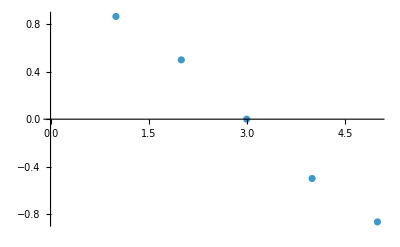

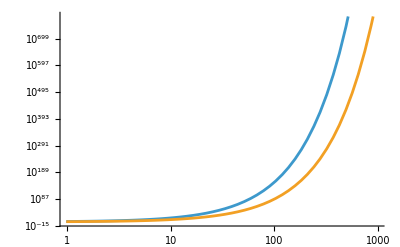

```mathematica
Nmodes=5;
ListPlot[Table[Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}]]
LogLogPlot[{Exp[4 0.87 t],{Exp[4 0.5 t]}},{t,0,1000}]
```

```mathematica
Nmodes=3
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]]
Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes]

{{0,1},{-1,0}}.{{a,b},{c,d}}.{{0,1},{-1,0}}//MatrixForm
Gt={{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{-1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0}};
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]]
"Is G correct"
Gt==Transpose[CovarBasis[Nmodes]].G.CovarBasis[Nmodes]//FullSimplify
Gt//TraditionalForm
```

3

{{0,1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,-1,0}}

{{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1},{-1,0,0,0,0,0},{0,-1,0,0,0,0},{0,0,-1,0,0,0}}

(-d | c
b | -a)

{{0,1,0,0,0,0},{-1,0,0,0,0,0},{0,0,0,1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,1},{0,0,0,0,-1,0}}

Is G correct

False

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

```mathematica
(* BUILD N PAIRS OF TWO_MODE SQUEEZERS, COVARIANCE MATRIX WILL BE BLOCK DIAGONAL AND QFI WILL SCALE LINEARLY WITH N, CHECK WITH EVGENY PPT, but here we have collective squeezing because BKC. Do the Hamiltonian for SPDC, SPDC+beamsplitter at EP. is the scaling with number of modes better when adding the beamsplitter? idk *)
```

```mathematica
(* analytical calculations *)
Clear[g,χ]
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,0,ϕb=0,χ,ϕχ=0,{}];
EOM//TraditionalForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
eigs=Eigensystem[DM]
S=Transpose[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
TrS=Inverse[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
InS=Transpose[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
InTrS=Inverse[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
Σin=CovarBasis[Nmodes].S.TrS.Transpose[CovarBasis[Nmodes]];
Σin//FullSimplify//TraditionalForm
InΣin=CovarBasis[Nmodes].InTrS.InS.Transpose[CovarBasis[Nmodes]];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Fcov=-1/2 Tr[InΣin.G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify
n//FullSimplify
```

(0 | 0 | 0 | χ
0 | 0 | χ | 0
0 | χ | 0 | 0
χ | 0 | 0 | 0)

{{-χ,-χ,χ,χ},{{0,0,1,1},{-1,1,0,0},{0,0,-1,1},{1,1,0,0}}}

(cosh(2 t χ) | 0 | sinh(2 t χ) | 0
0 | cosh(2 t χ) | 0 | -sinh(2 t χ)
sinh(2 t χ) | 0 | cosh(2 t χ) | 0
0 | -sinh(2 t χ) | 0 | cosh(2 t χ))

4 Cosh[t χ]^2

4 Sinh[t χ]^2

```mathematica
(* analytical calculations *)
Clear[g,χ]
Nmodes=3;
EOM=BosonicKitaevChain[Nmodes,0,ϕb=0,χ,ϕχ=0,{}];
EOM//TraditionalForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
eigs=Eigensystem[DM]
S=Transpose[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
TrS=Inverse[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
InS=Transpose[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
InTrS=Inverse[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
Σin=CovarBasis[Nmodes].S.TrS.Transpose[CovarBasis[Nmodes]];
Σin//FullSimplify//TraditionalForm
InΣin=CovarBasis[Nmodes].InTrS.InS.Transpose[CovarBasis[Nmodes]];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Fcov=-1/2 Tr[InΣin.G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify
n//FullSimplify
```

(0 | 0 | 0 | 0 | χ | 0
0 | 0 | 0 | χ | 0 | χ
0 | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | 0
χ | 0 | χ | 0 | 0 | 0
0 | χ | 0 | 0 | 0 | 0)

{{-√2 χ,-√2 χ,√2 χ,√2 χ,0,0},{{0,0,0,1,√2,1},{1,-√2,1,0,0,0},{0,0,0,1,-√2,1},{1,√2,1,0,0,0},{0,0,0,-1,0,1},{-1,0,1,0,0,0}}}

(cosh^2(√2 t χ) | 0 | (sinh(2 √2 t χ))/(√2) | 0 | sinh^2(√2 t χ) | 0
0 | cosh^2(√2 t χ) | 0 | -(sinh(2 √2 t χ))/(√2) | 0 | sinh^2(√2 t χ)
(sinh(2 √2 t χ))/(√2) | 0 | cosh(2 √2 t χ) | 0 | (sinh(2 √2 t χ))/(√2) | 0
0 | -(sinh(2 √2 t χ))/(√2) | 0 | cosh(2 √2 t χ) | 0 | -(sinh(2 √2 t χ))/(√2)
sinh^2(√2 t χ) | 0 | (sinh(2 √2 t χ))/(√2) | 0 | cosh^2(√2 t χ) | 0
0 | sinh^2(√2 t χ) | 0 | -(sinh(2 √2 t χ))/(√2) | 0 | cosh^2(√2 t χ))

4 Cosh[√2 t χ]^2

4 Sinh[√2 t χ]^2

```mathematica
(* analytical calculations *)
Clear[g,χ]
Nmodes=4;
EOM=BosonicKitaevChain[Nmodes,0,ϕb=0,χ,ϕχ=0,{}];
EOM//TraditionalForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
eigs=Eigensystem[DM]
S=Transpose[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
TrS=Inverse[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
InS=Transpose[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
InTrS=Inverse[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
Σin=CovarBasis[Nmodes].S.TrS.Transpose[CovarBasis[Nmodes]];
Σin//FullSimplify//TraditionalForm
InΣin=CovarBasis[Nmodes].InTrS.InS.Transpose[CovarBasis[Nmodes]];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Fcov=-1/2 Tr[InΣin.G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify
n//FullSimplify
```

(0 | 0 | 0 | 0 | 0 | χ | 0 | 0
0 | 0 | 0 | 0 | χ | 0 | χ | 0
0 | 0 | 0 | 0 | 0 | χ | 0 | χ
0 | 0 | 0 | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | 0 | 0 | 0
χ | 0 | χ | 0 | 0 | 0 | 0 | 0
0 | χ | 0 | χ | 0 | 0 | 0 | 0
0 | 0 | χ | 0 | 0 | 0 | 0 | 0)

{{1/2 (-1-√5) χ,1/2 (-1-√5) χ,1/2 (1+√5) χ,1/2 (1+√5) χ,1/2 (1-√5) χ,1/2 (1-√5) χ,1/2 (-1+√5) χ,1/2 (-1+√5) χ},{{0,0,0,0,1,1/2 (1+√5),1/2 (1+√5),1},{-1,1/2 (1+√5),1/2 (-1-√5),1,0,0,0,0},{0,0,0,0,-1,1/2 (1+√5),1/2 (-1-√5),1},{1,1/2 (1+√5),1/2 (1+√5),1,0,0,0,0},{0,0,0,0,-1,1/2 (1-√5),1/2 (-1+√5),1},{1,1/2 (1-√5),1/2 (1-√5),1,0,0,0,0},{0,0,0,0,1,1/2 (1-√5),1/2 (1-√5),1},{-1,1/2 (1-√5),1/2 (-1+√5),1,0,0,0,0}}}

(cosh(t χ) cosh(√5 t χ)-(sinh(t χ) sinh(√5 t χ))/(√5) | 0 | (2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | sinh(t χ) cosh(√5 t χ)-(sinh(√5 t χ) cosh(t χ))/(√5) | 0
0 | cosh(t χ) cosh(√5 t χ)-(sinh(t χ) sinh(√5 t χ))/(√5) | 0 | -(2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | (sinh(√5 t χ) cosh(t χ))/(√5)-sinh(t χ) cosh(√5 t χ)
(2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (sinh(t χ) sinh(√5 t χ))/(√5)+cosh(t χ) cosh(√5 t χ) | 0 | sinh(t χ) cosh(√5 t χ)+(sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0
0 | -(2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (sinh(t χ) sinh(√5 t χ))/(√5)+cosh(t χ) cosh(√5 t χ) | 0 | sinh(t χ) (-cosh(√5 t χ))-(sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5)
(2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | sinh(t χ) cosh(√5 t χ)+(sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (sinh(t χ) sinh(√5 t χ))/(√5)+cosh(t χ) cosh(√5 t χ) | 0 | (2 sinh(√5 t χ) cosh(t χ))/(√5) | 0
0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | sinh(t χ) (-cosh(√5 t χ))-(sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (sinh(t χ) sinh(√5 t χ))/(√5)+cosh(t χ) cosh(√5 t χ) | 0 | -(2 sinh(√5 t χ) cosh(t χ))/(√5)
sinh(t χ) cosh(√5 t χ)-(sinh(√5 t χ) cosh(t χ))/(√5) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | (2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | cosh(t χ) cosh(√5 t χ)-(sinh(t χ) sinh(√5 t χ))/(√5) | 0
0 | (sinh(√5 t χ) cosh(t χ))/(√5)-sinh(t χ) cosh(√5 t χ) | 0 | (2 sinh(t χ) sinh(√5 t χ))/(√5) | 0 | -(2 sinh(√5 t χ) cosh(t χ))/(√5) | 0 | cosh(t χ) cosh(√5 t χ)-(sinh(t χ) sinh(√5 t χ))/(√5))

(-2+Cosh[2 (-1+√5) t χ]+Cosh[2 (1+√5) t χ])/(-2+2 Cosh[t χ] Cosh[√5 t χ])

-4+4 Cosh[t χ] Cosh[√5 t χ]

```mathematica
Clear[g,χ]
e=Eigensystem[DM];
P=Transpose[e[[2]]];

S==P.MatrixExp[DiagonalMatrix[e[[1]]] t].Inverse[P]//FullSimplify
Inverse[S]==P.MatrixExp[-DiagonalMatrix[e[[1]]] t].Inverse[P]//FullSimplify
Transpose[S]==Transpose[Inverse[P]].MatrixExp[DiagonalMatrix[e[[1]]] t].Transpose[P]//FullSimplify
```

True

True

True

(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

4+4 g^2 t^2

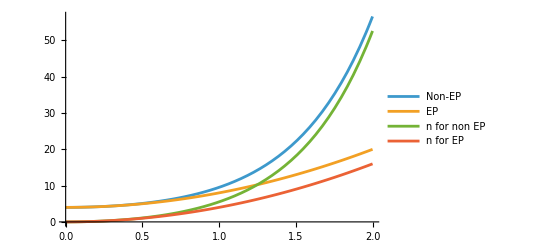

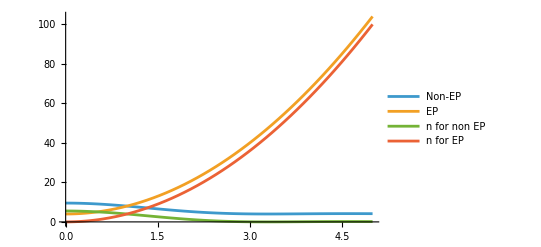

Normal points win when squeezing is higher than beamsplitter, EP points win when squeezing is lower than beam-splitter

EP is the onset of exponentially growing QFI

Scaling with time

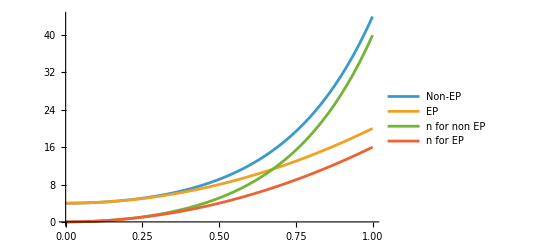

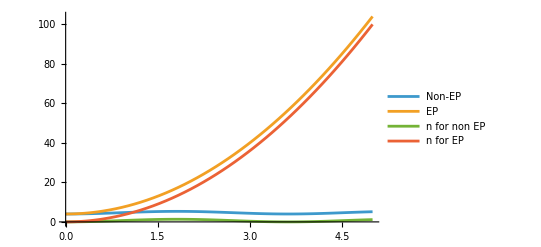

```mathematica
(*Doesn't generically win over DP*)
Clear[g,χ];
Fcov/n//FullSimplify;
QFI2ppNonEP=Fcov/n/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
Limit[QFI2ppNonEP,χ->g]

g=0;
Plot[{-(2 (-2 g^2+χ^2+χ^2 Cosh[2 √(-g^2+χ^2)]))/((g-χ) (g+χ)),4+4 χ^2,(4 χ^2 Sinh[ √(-g^2+χ^2)]^2)/(-g^2+χ^2),4 χ^2},{χ,0,2},PlotRange->All,PlotLegends->{"Non-EP","EP","n for non EP","n for EP"}]

Clear[g,χ];χ=1;
Plot[{-(2 (-2 g^2+χ^2+χ^2 Cosh[2 √(-g^2+χ^2)]))/((g-χ) (g+χ)),4+4 g^2,(4 χ^2 Sinh[ √(-g^2+χ^2)]^2)/(-g^2+χ^2),4 g^2},{g,0,5},PlotRange->All,PlotLegends->{"Non-EP","EP","n for non EP","n for EP"}]

"Normal points win when squeezing is higher than beamsplitter, EP points win when squeezing is lower than beam-splitter"
"EP is the onset of exponentially growing QFI"
"Scaling with time"
Clear[g,χ];χ=2;g=1;
Plot[{-(2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]))/((g-χ) (g+χ)),4+4 χ^2 t^2,(4 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2),4 χ^2 t^2},{t,0,1},PlotRange->All,PlotLegends->{"Non-EP","EP","n for non EP","n for EP"}]
Clear[g,χ];χ=.5;g=1;
Plot[{-(2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]))/((g-χ) (g+χ)),4+4 g^2 t^2,(4 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2),4 g^2 t^2},{t,0,5},PlotRange->All,PlotLegends->{"Non-EP","EP","n for non EP","n for EP"}]
```

```mathematica
Clear[g,χ]
Nmodes=3;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
eigs=Eigensystem[DM];
S=Transpose[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
TrS=Inverse[eigs[[2]]].MatrixExp[DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
InS=Transpose[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].Inverse[Transpose[eigs[[2]]]];
InTrS=Inverse[eigs[[2]]].MatrixExp[-DiagonalMatrix[eigs[[1]] ] t].eigs[[2]];
Σin=CovarBasis[Nmodes].S.TrS.Transpose[CovarBasis[Nmodes]];
InΣin=CovarBasis[Nmodes].InTrS.InS.Transpose[CovarBasis[Nmodes]];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Fcov=-1/2 Tr[InΣin.G.Σin.G]-Nmodes;
n=1/2 (Tr[Σin]-2 Nmodes);
Fcov/n//FullSimplify
```

(4 (g^2-χ^2 Cosh[√2 t √(-g^2+χ^2)])^2)/((g^2-χ^2)^2)

4 (1+t^2 χ^2)^2

1+10 t^2 χ^2+8 t^4 χ^4+(16 t^6 χ^6)/9+(9 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

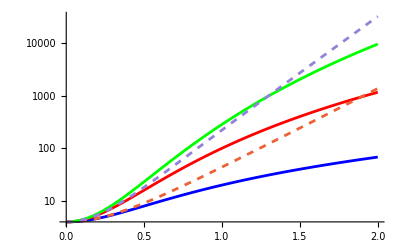

```mathematica
Fcov3/n3/.{x1->0,x2->0,x3->0,p1->0,p2->0,p3->0}//FullSimplify

Fcov4/n4/.{x1->0,x2->0,x3->0,x4->0,p1->0,p2->0,p3->0,p4->0}//FullSimplify
g=1;χ=2;
LogPlot[{4+4 χ^2 t^2,4 (1+t^2 χ^2)^2,1+10 t^2 χ^2+8 t^4 χ^4+(16 t^6 χ^6)/9+(9 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4),-(2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]))/((g-χ) (g+χ)),(4 (g^2-χ^2 Cosh[√2 t √(-g^2+χ^2)])^2)/((g^2-χ^2)^2)},{t,0,2},PlotStyle->{Blue,Red,Green,Dashed,Dashed}]
```

```mathematica
-(2 (-2 g^2+χ^2+χ^2 Cosh[2 √(-g^2+χ^2)]))/((g-χ) (g+χ))/.χ->0
```

8/3

```mathematica
(* non-zero EP *)
Clear[g,χ]
Nmodes=2;
EOM={{-I ω1,g,ξ1,χ},{-g,-I ω2,χ,ξ2},{ξ1,χ,I ω1,g},{χ,ξ2,-g,I ω2}};
EOM//TraditionalForm;
EOMEP=EOM/.{ξ2->0,ω2->0,ω1->0,ξ1->2 g,χ->0};
EOMEP//Eigensystem

DM=QT[Nmodes].(EOMEP).ConjugateTranspose[QT[Nmodes]]
S=MatrixExp[DM t]//FullSimplify
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{FcovEP,FdispEP,n2EP}={1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify};
(FcovEP+FdispEP)/n2EP/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
```

{{-g,-g,g,g},{{-1,-1,1,1},{0,0,0,0},{-1,1,-1,1},{0,0,0,0}}}

{{2 g,g,0,0},{-g,0,0,0},{0,0,-2 g,g},{0,0,-g,0}}

{{ⅇ^(g t) (1+g t),ⅇ^(g t) g t,0,0},{-ⅇ^(g t) g t,ⅇ^(g t) (1-g t),0,0},{0,0,ⅇ^(-g t) (1-g t),ⅇ^(-g t) g t},{0,0,-ⅇ^(-g t) g t,ⅇ^(-g t) (1+g t)}}

(-1+(1+8 g^2 t^2+8 g^4 t^4) Cosh[4 g t])/(-1+(1+2 g^2 t^2) Cosh[2 g t])

```mathematica
Clear[g,ω1,ω2,ξ1,χ,ξ2]
Nmodes=2;
EOM={{-I ω1,g,ξ1,χ},{-g,-I ω2,χ,ξ2},{ξ1,χ,I ω1,g},{χ,ξ2,-g,I ω2}}
EOM=EOM/.{ξ2->0,ω2->0,ω1->0,χ->0};
EOM//Eigensystem
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
Fcov=1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
n2=1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
Fcov/n2
```

{{-ⅈ ω1,g,ξ1,χ},{-g,-ⅈ ω2,χ,ξ2},{ξ1,χ,ⅈ ω1,g},{χ,ξ2,-g,ⅈ ω2}}

{{1/2 (-ξ1-√(-4 g^2+ξ1^2)),1/2 (ξ1-√(-4 g^2+ξ1^2)),1/2 (-ξ1+√(-4 g^2+ξ1^2)),1/2 (ξ1+√(-4 g^2+ξ1^2))},{{-(ξ1+√(-4 g^2+ξ1^2))/(2 g),-1,-(-ξ1-√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1-√(-4 g^2+ξ1^2))/(2 g),1,-(ξ1-√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1-√(-4 g^2+ξ1^2))/(2 g),-1,-(-ξ1+√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1+√(-4 g^2+ξ1^2))/(2 g),1,-(ξ1+√(-4 g^2+ξ1^2))/(2 g),1}}}

1/((-4 g^2+ξ1^2)^2)(-2 (-4 g^2+ξ1^2)^2+16 g^2 (2 g^2+ξ1^2) Cosh[2 t ξ1]+ξ1^4 (Cosh[2 t (ξ1-√(-4 g^2+ξ1^2))]+Cosh[2 t (ξ1+√(-4 g^2+ξ1^2))])-16 g^2 ξ1^2 (Cosh[t (-2 ξ1+√(-4 g^2+ξ1^2))]+Cosh[t (2 ξ1+√(-4 g^2+ξ1^2))]))

-2+(2 Cosh[t ξ1] (4 g^2-ξ1^2 Cosh[t √(-4 g^2+ξ1^2)]))/(4 g^2-ξ1^2)

(-2 (-4 g^2+ξ1^2)^2+16 g^2 (2 g^2+ξ1^2) Cosh[2 t ξ1]+ξ1^4 (Cosh[2 t (ξ1-√(-4 g^2+ξ1^2))]+Cosh[2 t (ξ1+√(-4 g^2+ξ1^2))])-16 g^2 ξ1^2 (Cosh[t (-2 ξ1+√(-4 g^2+ξ1^2))]+Cosh[t (2 ξ1+√(-4 g^2+ξ1^2))]))/((-4 g^2+ξ1^2)^2 (-2+(2 Cosh[t ξ1] (4 g^2-ξ1^2 Cosh[t √(-4 g^2+ξ1^2)]))/(4 g^2-ξ1^2)))

```mathematica
Clear[g,χ]
n2EP/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
n2
```

-2+(2+4 g^2 t^2) Cosh[2 g t]

-2+(2 Cosh[t ξ1] (4 g^2-ξ1^2 Cosh[t √(-4 g^2+ξ1^2)]))/(4 g^2-ξ1^2)

```mathematica
"At an EP the real part of eigenvalue is reduced, minimizing exponential growth"
```

At an EP the real part of eigenvalue is reduced, minimizing exponential growth

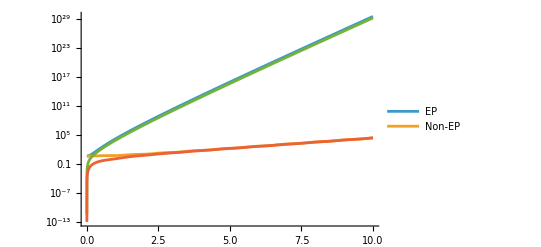

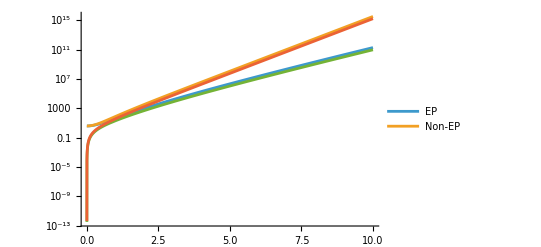

```mathematica
g=3;ξ1=1;
LogPlot[{(-1+(1+8 g^2 t^2+8 g^4 t^4) Cosh[4 g t])/(-1+(1+2 g^2 t^2) Cosh[2 g t]),Fcov/n2,n2EP/.{x1->0,x2->0,p1->0,p2->0},n2},{t,0,10},PlotLegends->{"EP","Non-EP"}]

Clear[g,ξ1]
g=1;ξ1=2.3;
LogPlot[{(-1+(1+8 g^2 t^2+8 g^4 t^4) Cosh[4 g t])/(-1+(1+2 g^2 t^2) Cosh[2 g t])/.g->ξ1/2,Fcov/n2,n2EP/.{x1->0,x2->0,p1->0,p2->0},n2},{t,0,10},PlotLegends->{"EP","Non-EP"}]
```